# L0 Solenoid Modeling

```mathematica
root=NotebookDirectory[]
```

/Volumes/user/cem52/erl/CERL/lattice_devel/Phase1B/model/a1/solenoid/

```mathematica
scratchdir="~/Desktop/";
```

```mathematica
rawFilename="solenoid_OUTSF7.TXT";
```

```mathematica
outputFilename = "in.solenoid_grid.bmad";
```

```mathematica
cLightN=299792458.
```

2.99792×10^8

## Options

```mathematica
myplotoptions={BaseStyle->{FontSize->15}, Frame->True};
SetOptions[Plot,myplotoptions];
SetOptions[ListPlot,myplotoptions];
SetOptions[ListLogPlot,myplotoptions];
SetOptions[ListVectorPlot,myplotoptions];
SetOptions[ListDensityPlot,myplotoptions];
```

## raw grid data

https://wiki.lepp.cornell.edu/lepp/bin/view/ERL/Private/SolenoidSLAFieldMap
L0solenoid_L60_OUTSF7.TXT: OUTSF7.TXT file with the total longitudinal field length of 60 cm. Rmax is 50.0 mm, and the increments of R is 1 mm. The increments of Z is 1 mm.

-Graphics-
-Graphics-

```mathematica
rawgriddat=Import[root<>rawFilename, "Table", "HeaderLines"->27];
```

```mathematica
rawgriddat[[1;;8]]//Grid
```

Magnetic | fields | for | a | rectangular | area | with | corners | at:
(Rmin,Zmin) | = | (0.0,-30) |  |  |  |  |  | 
(Rmax,Zmax) | = | (5,30) |  |  |  |  |  | 
R | and | Z | increments: | 50 | 600 |  |  | 
 |  |  |  |  |  |  |  | 
R | Z | Br | Bz | |B| | A | dBz/dr | dBr/dz | Field
(cm) | (cm) | (G) | (G) | (G) | (G-cm) | (G/cm) | (G/cm) | Index
0. | -30. | 0. | 0.447726 | 0.447726 | 0. | 0. | 0. | 0.

```mathematica
xC=1;
zC=2;
BxC=3;
BzC=4;
AC=5;
griddat={10^-2(*m/cm*)#[[1]], 10^-2(*m/cm*)#[[2]](*m*), 10^-4(*T/G*)#[[3]],  10^-4 (*T/G*)#[[4]], 10^-4(*T/G*)10^-2(*m/cm*)#⟦6⟧}&/@rawgriddat[[8;;]];
```

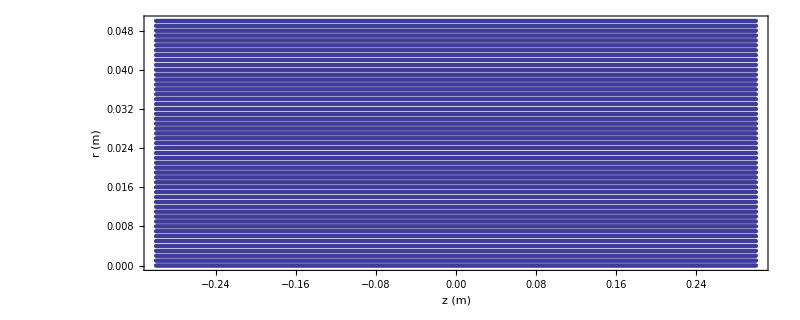

```mathematica
ListPlot[{#⟦zC ⟧, #⟦xC ⟧}&/@griddat, FrameLabel->{"z (m)", "r (m)"}, AspectRatio->Automatic, ImageSize->800]
```

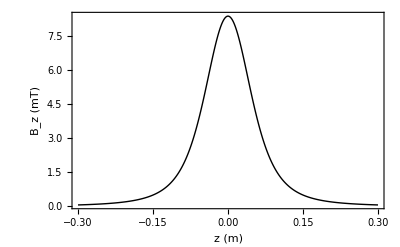

```mathematica
ListPlot[{ #⟦zC ⟧, 10^3#⟦BzC⟧}&/@Select[griddat, #[[xC]]<0.0001&], PlotStyle->Black, Joined->True, FrameLabel->{"z (m)", "B_z (mT)"}]
```

```mathematica
dat0=Select[griddat,# ⟦xC⟧<0.0001&];
dat1=Select[griddat,0.0001<# ⟦xC⟧<0.0011&];Length[dat1]
```

601

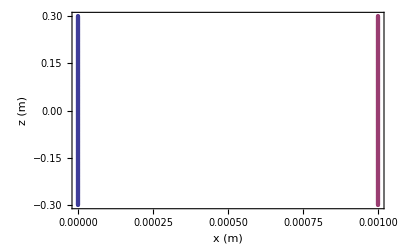

```mathematica
ListPlot[{{#⟦xC ⟧, #⟦zC ⟧}&/@dat0, {#⟦xC ⟧, #⟦zC ⟧}&/@dat1}, FrameLabel->{"x (m)", "z (m)"}]
```

```mathematica
{Min[dat0[[All,xC]]], Max[dat0[[All,xC]]], Min[dat1[[All,xC]]], Max[dat1[[All,xC]]]}
```

{0.,0.,0.001,0.001}

```mathematica
{Min[dat0[[All,zC]]], Max[dat0[[All,zC]]]}
```

{-0.3,0.3}

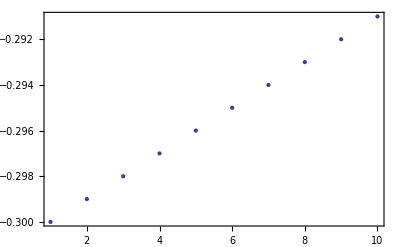

```mathematica
ListPlot[dat0[[1;;10,zC]],PlotRange->All]
```

```mathematica
dat0[[1;;3,zC]]
```

{-0.3,-0.299,-0.298}

## Verify Grid

```mathematica
refdat=griddat;
```

```mathematica
xlist=Sort[#[[xC]]&/@refdat, #1<#2&];xlist=Intersection[xlist,xlist];
zlist=Sort[#[[zC]]&/@refdat, #1<#2&];zlist=Intersection[zlist,zlist];
xmax = Max[xlist];xmin = Min[xlist];xsize=xmax-xmin;
zmax = Max[zlist];zmin = Min[zlist];zsize=zmax-zmin;
```

```mathematica
Grid[{{,"min (m)","max (m)"},{"x: ",xmin,xmax}, {"z: ",zmin,zmax}}, Frame->True, Alignment->Left]
```

| min (m) | max (m)
x:  | 0. | 0.05
z:  | -0.3 | 0.3

```mathematica
Δz = 0.001;
Δx = 0.001;
izof[z_]:=Round[(z -zmin)/Δz];
ixof[x_]:=Round[(x -xmin)/Δx];
zof[iz_]:=zmin + iz Δz;
xof[ix_]:=xmin + ix Δx;
```

```mathematica
izof[zmin]
```

0

```mathematica
ixof[xmin]
```

0

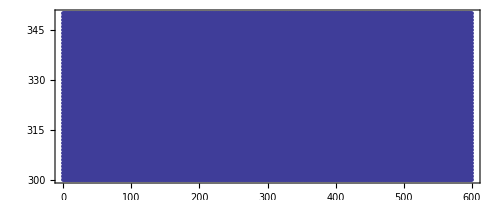

```mathematica
ListPlot[{izof[#[[zC]]],izof[#[[xC]]]}&/@refdat, AspectRatio->Automatic]
```

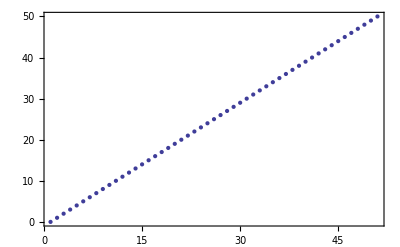

```mathematica
ListPlot[ixof/@xlist]
```

```mathematica
Length[xlist]
```

51

```mathematica
Length[zlist]
```

601

```mathematica
ListPointPlot3D[{{ixof[#⟦xC⟧],izof[#⟦zC⟧] ,#[[BzC]]}&/@refdat, {ixof[#⟦xC⟧],izof[#⟦zC⟧] ,#[[BxC]]}&/@refdat}, PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue},{PointSize[Tiny], Red}},AxesLabel->{"x index", "z index", "B (T)"}, BaseStyle->{FontSize->15}]
```

-Graphics3D-

```mathematica
array=Table[0, {Length[xlist]}, {Length[zlist]}];
(array[[ ixof[#⟦xC⟧]+1,izof[#⟦zC⟧] +1]]=#[[BzC]])&/@refdat;
```

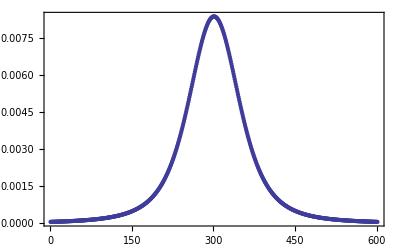

```mathematica
ListPlot[array[[1,All]]]
```

```mathematica
ListDensityPlot[array, DataRange->{{zmin,zmax}, {xmin,xmax}}, PlotRange->All]
```

-Graphics-

## Make Bmad Grid

```mathematica
fieldmapdir = root;
tmpdir = "~/Desktop/";
```

```mathematica
(*scale field by the maximum on-axis Bz*)
fieldmax=Max[Select[refdat, #⟦xC⟧ ==0&][[All, BzC]]];
factor = 1/fieldmax;
note={"! Maximum on-axis Bz scaled to 1 T"};
```

```mathematica
(*pt format: pt(ir, iz) = ( (ErRe,ErIm), (0,0), (EzRe,EzIm), (0,0), (BrRe,BrIm), (0,0), (BϕRe, BϕIm) , (0,0) ) *)
MakeBmadGrid[dat_]:=Module[{header, body, ptlist},
header = {"{ "};
body = {
{"type = rotationally_symmetric_rz,"},
{"r0 = (",xmin,"," ,0 ,")," },
{"dr = (", Δx,",", Δz, "),"}
};

ptlist ={
"pt(", ixof[ #⟦xC⟧  ], "," ,izof[#⟦zC⟧]  ,") = ( ",
	"0, 0, 0, ",
	factor*#⟦BxC⟧,", 0, ",factor*#⟦BzC⟧,")", ","}&/@dat; 
ptlist[[-1,-1]] = "}";
Join[header,note, body,  ptlist]

]
```

```mathematica
paddat = Table[ { x, zmax + Δz, 0, 0}, {x, xlist}];
griddata=MakeBmadGrid[refdat ~Join~paddat];
```

```mathematica
Export[tmpdir <>outputFilename  ,griddata, "Table", "FieldSeparators"->""];
Run["mv "<>tmpdir <>outputFilename<>" "<>fieldmapdir <>outputFilename];
```

```mathematica
fieldmax
```

0.00835383

## Make GPT file for ASCI2GDF

```mathematica
gptdat=Select[refdat, ((Abs[#⟦zC⟧]≤ 0.3)&& #⟦xC⟧≤ 0.05 )&];
```

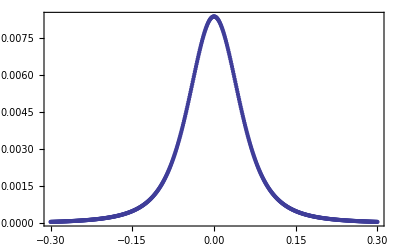

```mathematica
ListPlot[{#⟦zC⟧, #⟦BzC⟧}&/@Select[gptdat, #⟦xC⟧==0&], PlotRange->All]
```

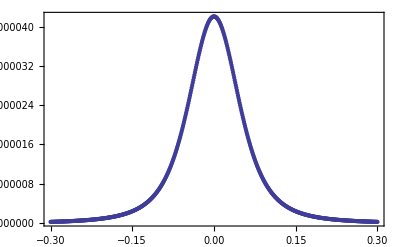

```mathematica
ListPlot[{#⟦zC⟧,#⟦AC⟧}&/@Select[gptdat, #⟦xC⟧==0.01&], PlotRange->All]
```

```mathematica
gptlabels={
{"# New solenoid"},
{"# On-axis Bz scaled to 1 T"},
{"# R(m)", "Z(m)",  "Br(T)", "Bz(T)", "|B|(T)", "A(T*m)"},
{"R", "Z", "Br", "Bz", "|B|", "A"}
};
```

```mathematica
gptoutdat={#⟦xC⟧, #⟦zC⟧,factor #⟦BxC⟧,factor#⟦BzC⟧,factor Sqrt[#⟦BxC⟧^2+#⟦BzC⟧^2],factor #⟦AC⟧}&/@gptdat;
```

```mathematica
file="solenoid_SLA_L60_new_for_ASCI2GDF.txt";
Export[tmpdir<>file, Join[gptlabels, gptoutdat], "Table"];
Run["mv "<>tmpdir<>file<>" "<>root<>file]
```

0

## EM Field query

```mathematica
fieldquerydir=root;
```

```mathematica
it = 1;
ix = 2;
iy =3;
is = 4;
iEx=5;
iEy=6;
iEs=7;
iBx=8;
iBy=9;
iBs=10;
```

### Field on axis

```mathematica
selebeg=0.1;

smin =0+selebeg;
smax = 0.6+selebeg;
myt=0;
myx=0.00;
myy=0.0;
sampledat=Table[{myt, myx, myy, s}, {s, smin, smax, (smax-smin)/(1024-1)}];
Export[scratchdir<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"];
Run["mv "<>scratchdir<>"querypoints.dat"<>" "<>root<>"querypoints.dat"]
```

0

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];
```

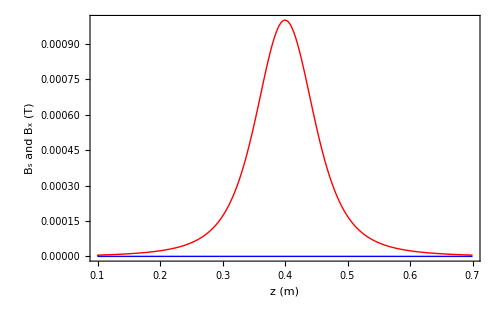

```mathematica
g1=ListPlot[{#[[is]],#[[iBs]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "E_x (MV/m)"}, PlotStyle->Red];
g2=ListPlot[{#[[is]], #[[iBx]]}&/@dat, Joined->True,PlotRange->All, Frame->True, BaseStyle->{FontSize->15}, FrameLabel->{"s (m)", "c B_y (MV/m)"}, PlotStyle->Blue];
Show[g1,g2, PlotRange->All, FrameLabel->{"z (m)", "B_s and B_x (T)"}, ImageSize->500]
```

```mathematica
Export[root<>"z_Bz_on_axis.dat", {#[[is]]-selebeg,#[[iBs]]}&/@dat, "Table"];
```

### Field on a flat grid

```mathematica
selebeg=0.1;

smin =0+selebeg;
smax = 0.6+selebeg;
myt=0;
myx=0.03;
xmin=0;
xmax = 0.05;
nx=50;
ns=200;
xstep=(xmax-xmin)/(nx-1);
 sstep=(smax-smin)/(ns-1);

isof[s_]:=Round[(s-smin)/sstep];
ixof[x_]:=Round[(x -xmin)/xstep];
zof[is_]:=smin + is sstep;
xof[ix_]:=xmin + ix xstep;

sampledat=Flatten[Table[{myt, x, myy, s}, {x,xmin,xmax,xstep},{s, smin, smax,sstep}], 1];Length[sampledat]
```

10000

```mathematica
Export[scratchdir<>"querypoints.dat",Join[{{Length[sampledat]}}, sampledat],  "Table"];
Run["mv "<>scratchdir<>"querypoints.dat"<>" "<>root<>"querypoints.dat"]
```

0

```mathematica
dat=Import[root<>"querypoints.out",  "Table"][[2;;]];Length[dat]
```

10000

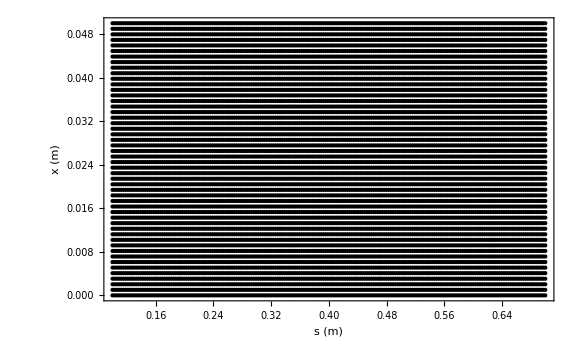

```mathematica
ListPlot[ {#[[is]], #[[ix]]}&/@dat, Frame->True, FrameLabel->{"s (m)", "x (m)"}, BaseStyle->{FontSize->15}, PlotStyle->Black]
```

```mathematica
Max[dat[[All, iBs]]]
```

0.0015059

```mathematica
ListPointPlot3D[{{#⟦is⟧, #⟦ix⟧, #⟦iBs⟧}&/@dat, {#⟦is⟧, #⟦ix⟧, #⟦iBx⟧}&/@dat} , PlotRange->All, PlotStyle->{{PointSize[Tiny], Blue},{PointSize[Tiny], Red}}]
```

-Graphics3D-

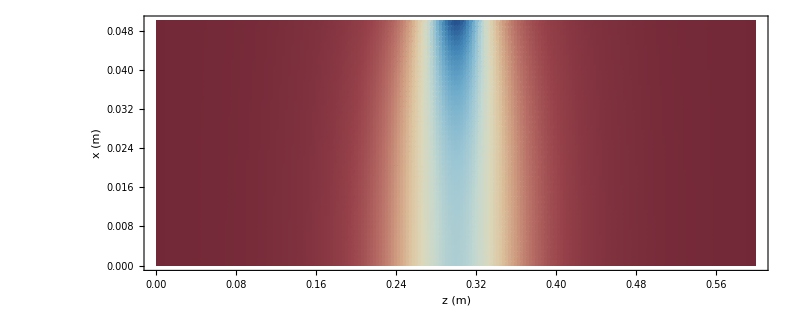

```mathematica
samplegridvalues=Table[0, {ns}, {nx}];
samplegridvalues⟦ isof[#⟦is⟧ ]+1, ixof[ #⟦ix⟧ ] +1⟧ =#⟦iBs⟧;&/@dat;
Show[ListDensityPlot[Transpose[samplegridvalues], DataRange->{{smin,smax}, {xmin,xmax}}, AspectRatio->Automatic, PlotRange->{{smin,smax}, {xmin,xmax}}, ColorFunction->"RedBlueTones", FrameLabel->{"z (m)", "x (m)"}],ImageSize->800]
```

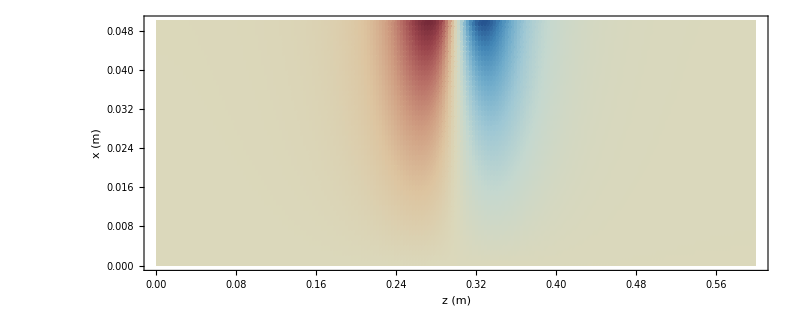

```mathematica
samplegridvalues=Table[0, {ns}, {nx}];
samplegridvalues⟦ isof[#⟦is⟧ ]+1, ixof[ #⟦ix⟧ ] +1⟧ =#⟦iBx⟧;&/@dat;
Show[ListDensityPlot[Transpose[samplegridvalues], DataRange->{{smin,smax}, {xmin,xmax}}, AspectRatio->Automatic, PlotRange->{{smin,smax}, {xmin,xmax},All}, ColorFunction->"RedBlueTones",FrameLabel->{"z (m)", "x (m)"}, PlotRange->All],ImageSize->800]
```

```mathematica
scale=1;
vdat={ {#[[is]], #[[ix]]}, {#[[iBs]],#⟦iBx⟧} } &/@ dat;Length[vdat]
```

10000

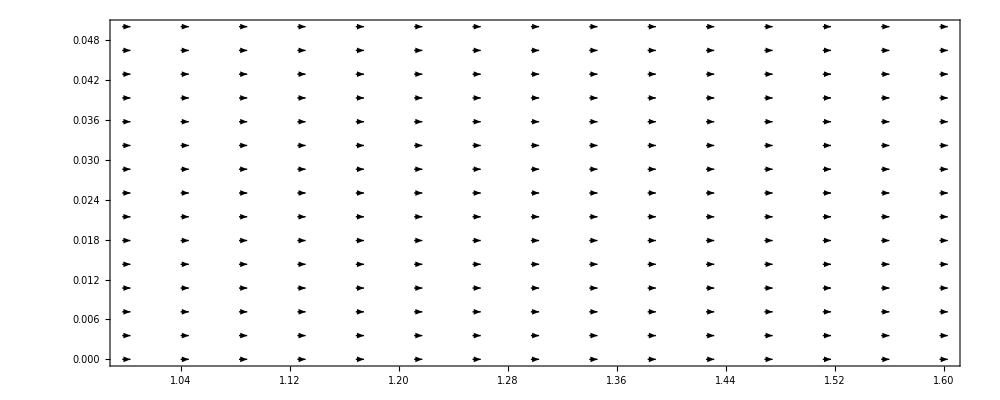

```mathematica
g2=ListVectorPlot[vdat, AspectRatio->Automatic, PlotRange->{{smin,smax},{xmin,xmax}},VectorScale->0.01,VectorPoints->Automatic,VectorStyle->{Black}, ImageSize->1000]
```

```mathematica
Show[g1,g2, FrameLabel->{"s (m)", "x (m)"}]
```

```mathematica
vdat3d={ {xmax/smax#[[4]], #[[2]], #[[3]]},{#[[7]],xmax/smax#[[5]],xmax/smax#[[6]]}} &/@ dat;Length[vdat3d]
```

```mathematica
vdat3d={ {#[[4]], #[[2]], #[[3]]},{0,0,0}} &/@ dat;Length[vdat3d]
```

```mathematica
vdat3d//StandardForm
```

```mathematica
ListVectorPlot3D[vdat3d]
```

```mathematica
ListPlot3D[{ {#[[4]], #[[2]], #[[3]]},{0,0,0}} &/@ dat]
```